```mathematica
n = 5
data ={
{1, 3-0.1n}, 
{2, 3.5+0.1n}, 
{3, 3.9+0.1n}, 
{4, 4.6+0.2n}, 
{5, 10.5 + 0.3n}, 
{6, 21.3 + 0.5n}, 
{7, 38.7 + 0.5n}, 
{8, 59.7 + n}
}
```

5

{{1,2.5},{2,4.},{3,4.4},{4,5.6},{5,12.},{6,23.8},{7,41.2},{8,64.7}}

```mathematica
line=Fit[data,{1,x},x]
```

-16.975+8.16667 x

```mathematica
quadr=Fit[data,{1,x,x^2},x]
```

13.65-10.2083 x+2.04167 x^2

```mathematica
cubic=Fit[data,{1,x,x^2,x^3},x]
```

1.85+2.06843 x-1.17652 x^2+0.238384 x^3

```mathematica
five = Fit[data,{1,x,x^2,x^3, x^4, x^5},x]
```

-6.225+14.3571 x-6.89643 x^2+1.3132 x^3-0.0814831 x^4+0.00179487 x^5

```mathematica
seven = Fit[data,{1,x,x^2,x^3, x^4, x^5, x^6, x^7},x]
```

32.9-78.9526 x+76.9061 x^2-36.4751 x^3+9.34653 x^4-1.31931 x^5+0.0973611 x^6-0.00293651 x^7

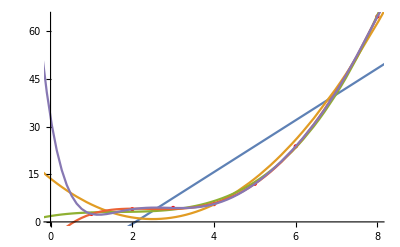

```mathematica
Show[ListPlot[data,PlotStyle->{PointSize[Medium],Red}],Plot[{line,quadr,cubic,five, seven},{x,-200, 200}]]
```

```mathematica
Column[Table[{line,quadr,cubic, five,seven}, {x, 1.5, 7.5, 1}]]
```

{-4.725,2.93125,3.11004,3.82684,2.76338}
{3.44167,0.889583,3.39261,4.07612,4.49541}
{11.6083,2.93125,4.89792,4.56211,4.51572}
{19.775,9.05625,9.05625,8.29336,8.07119}
{27.9417,19.2646,17.2979,17.0767,17.2712}
{36.1083,33.5563,31.0532,31.7326,31.6876}
{44.275,51.9313,51.7525,52.3104,52.4548}